# Determine if a set of linear equations Ax=b has a solution and what type of solution

```mathematica
Remove["Global`*"];
```

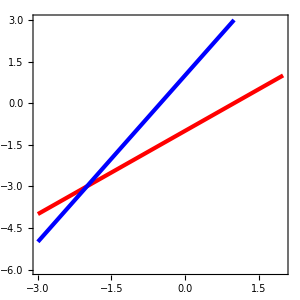

```mathematica
ContourPlot[{y==x-1,y==2 x+1},{x,-3,2},{y,-6,3},ContourStyle->{{Red,Thickness[0.01]},{Blue,Thickness[0.01]}},GridLinesStyle->Dashed,ImageSize->300]
```

```mathematica
a={{-2,1},{-1,1}};
```

```mathematica
b={1,-1};
```

```mathematica
{nRow,nCol}=Dimensions[a];
```

```mathematica
aRank=MatrixRank[a]
```

2

```mathematica
abRank=MatrixRank[Insert[a,b,-1]]
```

2

The above algorithm can now be run as follows

```mathematica
If[aRank<abRank,Print["System is no consistent, no exact solution"];
x=PseudoInverse[a].b,If[aRank==nCol,Print["System is consistent. Exact solution."];
x=LinearSolve[a,b],Print["consistent, rank deficient, infinite solutions"];
x=LinearSolve[a,b]]];
Print["Solution is x=",x];
```

System is consistent. Exact solution.

Solution is x={-2,-3}